```mathematica
ariasD[0] = 1;
ariasD[n_Integer?Positive] := ariasD[n] = Sum[2^((k (k - 1) - n (n - 1))/2) ariasD[k]/(n - k + 1)!, {k, 0, n - 1}]/(2^n - 1);
iFabiusF[x_] := Module[{prec = Precision[x], n, p, q, s, tol, w, y, z},
  If[x < 0, Return[0, Module]]; tol = 10^(-prec);
  z = SetPrecision[x, Infinity]; s = 1; y = 0;
  z = If[0 <= z <= 2, 1 - Abs[1 - z],
    q = Quotient[z, 2];
    If[ThueMorse[q] == 1, s = -1];
    1 - Abs[1 - z + 2 q]];
  While[z > 0,
   n = -Floor[RealExponent[z, 2]]; p = 2^n;
   z -= 1/p; w = 1;
   Do[w = ariasD[m] + p z w/(n - m + 1); p /= 2, {m, n}];
   y = w - y;
   If[Abs[w] < Abs[y] tol, Break[]]];
  SetPrecision[s Abs[y], prec]]
FabiusF[Infinity] = Interval[{-1, 1}];
FabiusF[x_?NumberQ] /; If[Im[x] == 0, TrueQ[Composition[BitAnd[#, # - 1] &, Denominator][x] == 0], False] := iFabiusF[x]
Derivative[n_Integer][FabiusF] := 2^(n (n + 1)/2) FabiusF[2^n #] &
SetAttributes[FabiusF, {NumericFunction, Listable}];
```

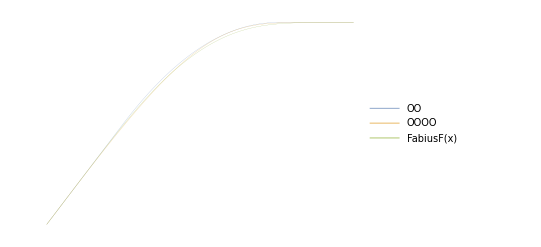

```mathematica
OO=(1/32)*((1-8*(x-1))*Abs[1-8*(x-1)]+(8*(x-1)+7)*Abs[8*(x-1)+7]-(8*(x-1)+5)*Abs[8*(x-1)+5]-(8*(x-1)+3)*Abs[8*(x-1)+3]+(8*(x-1)+1)*Abs[8*(x-1)+1]-(3-8*(x-1))*Abs[3-8*(x-1)]-(5-8*(x-1))*Abs[5-8*(x-1)]+(7-8*(x-1))*Abs[7-8*(x-1)]);
OOOO=-((0-(-1)^Floor[x/1+0.]*(Exp[-(1/(x-1*Floor[x/1]))]/(Exp[-(1/(x-1*Floor[x/1]))]+Exp[-(1/(1-(x-1*Floor[x/1])))]))+(-1)^Floor[x/1+0.]*(Exp[-(1/(1-(x-1*Floor[x/1])))]/(Exp[-(1/(x-1*Floor[x/1]))]+Exp[-(1/(1-(x-1*Floor[x/1])))])))/2)+0.5;
Plot[{OO,OOOO,FabiusF[x]},{x,0.5,1},ImageSize->Full,Axes->False,MaxRecursion->0,PlotPoints->1+2^8,PlotStyle->Thickness[0.00001],PlotLegends-> Placed["Expressions",{Center,Top}],PlotRangePadding->0]
```